## Initialization

```mathematica
Clear["Global`*"];
ClearSystemCache[];
SetDirectory[NotebookDirectory[]];
Install["Suave-Linux"];
```

## Functions

```mathematica
K[x_,y_,n_]:=2 √(x+y)P[x,y,n];
P[x_,y_,0]:=1;
P[x_,y_,1]:=1/3 (-2 x+y)
P[x_,y_,2]:=1/15 (8 x^2+y (-4 x+3 y));
```

```mathematica
f[x_,y_,μF_,n_]:=Q[x,y,μF,n]/(2 √(x+y))+(-1)^(n+1)Gamma[n+1]m^(2n+2)Log[x+y]+(-1)^(n)Gamma[n+1]m^(2n+2)Log[ft[x,y]]/.m->mn;
ft[x_,y_]:=(x+y) (2 m^2+y+√(y (4 m^2+y)))/.m->mn;
Q[x_,y_,μF_,0]:=-2 x^(3/2)-2 √x y-4 m (x+y)+y (√(((4 m^2+y) (x+y))/y)-4 μF)-4 x μF/.m->mn;
Q[x_,y_,μF_,1]:=1/2 y (2 m^2+y) √(((4 m^2+y) (x+y))/y)-2/3 (-2 x+y) (x+y) (2 m+√x+2 μF)/.m->mn;
Q[x_,y_,μF_,2]:=1/3 y √(((4 m^2+y) (x+y))/y) (-6 m^4+m^2 y+y^2)-2/15 (x+y) (8 x^2-4 x y+3 y^2) (2 m+√x+2 μF)/.m->mn;
```

```mathematica
tpp[q0_,μF_]:=2 (q0 x+x^2+√(x (2 mn+x) (q0+x) (2 mn+q0+x))+mn (q0+2 x))/.x->μF;
tpm[q0_,μF_]:=2 (q0 x+x^2-√(x (2 mn+x) (q0+x) (2 mn+q0+x))+mn (q0+2 x))/.x->μF;
tmp[q0_,μF_]:=tpp[-q0,μF]//Simplify;
tmm[q0_,μF_]:=tpm[-q0,μF]//Simplify;
```

```mathematica
tep[q0_,T_,mχ_]:=k0(k0-q0)-mχ^2+Sqrt[k0^2-mχ^2]Sqrt[(k0-q0)^2-mχ^2]/.k0->mχ+T;
tem[q0_,T_,mχ_]:=k0(k0-q0)-mχ^2-Sqrt[k0^2-mχ^2]Sqrt[(k0-q0)^2-mχ^2]/.k0->mχ+T;
```

```mathematica
Etp[q0_,t_]:=-(mn+q0/2)+Sqrt[(mn+q0/2)^2+(Sqrt[t]/2-mn*q0/Sqrt[t])^2];
Etm[q0_,t_]:=-(mn+q0/2)-Sqrt[(mn+q0/2)^2+(Sqrt[t]/2-mn*q0/Sqrt[t])^2];
```

```mathematica
coeff[T_,mχ_]:=1/(2^7 Pi^3k0*Sqrt[k0^2-mχ^2])/.k0->mχ+T;
M2[σ_,mn_,mχ_]:=σ*(16Pi*(mn^2+mχ^2));
```

```mathematica
Γ[T_,mχ_,μF_,σ_]:=convfact*coeff[T,mχ]M2[σ,mn,mχ]Part[Suave[Integr[q0,T,mχ,μF]//Re,{q0,0,T}, Verbose->0], 1,1];(*NIntegrate[(q0/Sqrt[q0^2+t]HeavisideTheta[tmp[q0,μF]-t]HeavisideTheta[t-tmm[q0,μF]])+(((Etm[q0,t]-μF)/Sqrt[q0^2+t]HeavisideTheta[tpp[q0,μF]-t]HeavisideTheta[t-tmp[q0,μF]])+((Etm[q0,t]-μF)/Sqrt[q0^2+t]HeavisideTheta[tmm[q0,μF]-t]HeavisideTheta[t-tpm[q0,μF]]))HeavisideTheta[μF(2mn+μF)/(mn+μF)-q0]+HeavisideTheta[q0-μF(2mn+μF)/(mn+μF)]((Etm[q0,t]-μF)/Sqrt[q0^2+t]HeavisideTheta[tpp[q0,μF]-t]HeavisideTheta[t-tpm[q0,μF]]),{q0,0,Min[T,q0/.FindRoot[tem[q0,T,mχ]==tpp[q0,μF],{q0,T/2}]]},{t,tem[q0,T,mχ],tep[q0,T,mχ]}];*)(*σ in cm^2, T mχ and μF in GeV*)
t[T_,mχ_,μF_,σ_]:=1/Γ[T,mχ,μF,σ];(*t inseconds*)
ty[T_,mχ_,μF_,σ_]:=stoy/Γ[T,mχ,μF,σ];(*t in years*)
```

```mathematica
DE[T_,mχ_,μF_,σ_]:=convfact*coeff[T,mχ]M2[σ,mn,mχ]Part[Suave[q0*Integr[q0,T,mχ,μF]//Re,{q0,0,T}, Verbose->0], 1,1]/Γ[T,mχ,μF,σ];
```

```mathematica
Res[q0_,T_,mχ_,μF_,max_,min_,Mmax_,mmin_][1]:=q0(K[q0^2,max,0]-K[q0^2,min,0])HeavisideTheta[Mmax-max]HeavisideTheta[min-mmin]HeavisideTheta[max-min];
Res[q0_,T_,mχ_,μF_,max_,min_,Mmax_,mmin_][2]:=-(f[q0^2,max,μF,0]-f[q0^2,min,μF,0])HeavisideTheta[Mmax-max]HeavisideTheta[min-mmin]HeavisideTheta[μF(2mn+μF)/(mn+μF)-q0]HeavisideTheta[max-min];
Res[q0_,T_,mχ_,μF_,max_,min_,Mmax_,mmin_][3]:=-(f[q0^2,max,μF,0]-f[q0^2,min,μF,0])HeavisideTheta[Mmax-max]HeavisideTheta[min-mmin]HeavisideTheta[q0-μF(2mn+μF)/(mn+μF)]HeavisideTheta[max-min];
```

```mathematica
Integrand[q0_,T_,mχ_,μF_][1,1]:=(Res[q0,T,mχ,μF,tep[q0,T,mχ],tem[q0,T,mχ],tmp[q0,μF],tmm[q0,μF]][1]+Res[q0,T,mχ,μF,tmp[q0,μF],tmm[q0,μF],tep[q0,T,mχ],tem[q0,T,mχ]][1]+Res[q0,T,mχ,μF,tep[q0,T,mχ],tmm[q0,μF],tmp[q0,μF],tem[q0,T,mχ]][1]+Res[q0,T,mχ,μF,tmp[q0,μF],tem[q0,T,mχ],tep[q0,T,mχ],tmm[q0,μF]][1])HeavisideTheta[(q0-μF) (-2 mn+q0-μF)];
Integrand[q0_,T_,mχ_,μF_][1,2]:=(Res[q0,T,mχ,μF,tep[q0,T,mχ],tem[q0,T,mχ],tpp[q0,μF],tmp[q0,μF]][2]+Res[q0,T,mχ,μF,tpp[q0,μF],tmp[q0,μF],tep[q0,T,mχ],tem[q0,T,mχ]][2]+Res[q0,T,mχ,μF,tep[q0,T,mχ],tmp[q0,μF],tpp[q0,μF],tem[q0,T,mχ]][2]+Res[q0,T,mχ,μF,tpp[q0,μF],tem[q0,T,mχ],tep[q0,T,mχ],tmp[q0,μF]][2])HeavisideTheta[(q0-μF) (-2 mn+q0-μF)];
Integrand[q0_,T_,mχ_,μF_][1,3]:=(Res[q0,T,mχ,μF,tep[q0,T,mχ],tem[q0,T,mχ],tmm[q0,μF],tpm[q0,μF]][2]+Res[q0,T,mχ,μF,tmm[q0,μF],tpm[q0,μF],tep[q0,T,mχ],tem[q0,T,mχ]][2]+Res[q0,T,mχ,μF,tep[q0,T,mχ],tpm[q0,μF],tmm[q0,μF],tem[q0,T,mχ]][2]+Res[q0,T,mχ,μF,tmm[q0,μF],tem[q0,T,mχ],tep[q0,T,mχ],tpm[q0,μF]][2])HeavisideTheta[(q0-μF) (-2 mn+q0-μF)];
Integrand[q0_,T_,mχ_,μF_][1,4]:=(Res[q0,T,mχ,μF,tep[q0,T,mχ],tem[q0,T,mχ],tpp[q0,μF],tpm[q0,μF]][2]+Res[q0,T,mχ,μF,tpp[q0,μF],tpm[q0,μF],tep[q0,T,mχ],tem[q0,T,mχ]][2]+Res[q0,T,mχ,μF,tep[q0,T,mχ],tpm[q0,μF],tpp[q0,μF],tem[q0,T,mχ]][2]+Res[q0,T,mχ,μF,tpp[q0,μF],tem[q0,T,mχ],tep[q0,T,mχ],tpm[q0,μF]][2])HeavisideTheta[-(q0-μF) (-2 mn+q0-μF)];
Integrand[q0_,T_,mχ_,μF_][2,2]:=(Res[q0,T,mχ,μF,tep[q0,T,mχ],tem[q0,T,mχ],tpp[q0,μF],tmp[q0,μF]][3]+Res[q0,T,mχ,μF,tpp[q0,μF],tmp[q0,μF],tep[q0,T,mχ],tem[q0,T,mχ]][3]+Res[q0,T,mχ,μF,tep[q0,T,mχ],tmp[q0,μF],tpp[q0,μF],tem[q0,T,mχ]][3]+Res[q0,T,mχ,μF,tpp[q0,μF],tem[q0,T,mχ],tep[q0,T,mχ],tmp[q0,μF]][3])HeavisideTheta[(q0-μF) (-2 mn+q0-μF)];
Integrand[q0_,T_,mχ_,μF_][2,4]:=(Res[q0,T,mχ,μF,tep[q0,T,mχ],tem[q0,T,mχ],tpp[q0,μF],0][3]+Res[q0,T,mχ,μF,tpp[q0,μF],tem[q0,T,mχ],tep[q0,T,mχ],0][3])HeavisideTheta[-(q0-μF) (-2 mn+q0-μF)];
```

```mathematica
Integr[q0_,T_,mχ_,μF_]:=Integrand[q0,T,mχ,μF][1,1]+Integrand[q0,T,mχ,μF][1,2]+Integrand[q0,T,mχ,μF][1,3]+Integrand[q0,T,mχ,μF][1,4]+Integrand[q0,T,mχ,μF][2,2]+Integrand[q0,T,mχ,μF][2,4];
```

```mathematica
Tp[T_,mχ_,μF_,σ_]:=T-DE[T,mχ,μF,σ];
tTh[T_,mχ_,μF_,σ_,Teq_]:=(
Clear[time,i,Tnow,dt];
time=0;
Tnow=T;
i=0;
Print["Start. T = ", Tnow, "GeV"];
While[Tnow>Teq,
i++;
Print["Calculating ", i, "-th scattering. T = ", FormatT[Tnow], " ",UnitT[Tnow],", t = ", Formatt[time], " ",Unitt[time] ];
dt=ty[Tnow,mχ,μF,σ];
While[!(NumericQ[dt]&&Arg[dt]<reg),Tnow=Tnow*0.9999;dt=ty[Tnow,mχ,μF,σ]; ];
time+=Re[dt];
Tnow=Tp[Tnow,mχ,μF,σ];
If[Im[Tnow]≠0,If[Arg[Tnow]<reg,Tnow=Re[Tnow],Print["Error, Complex T. T = ", FormatT[Tnow], " ",UnitT[Tnow]];Break[];]];
];
Print["Final scattering. T = ", FormatT[Tnow], " ",UnitT[Tnow],", t = ", Formatt[time], " ",Unitt[time] ];
Return[Tnow];
Clear[time,i,Tnow,dt];
)
```

```mathematica
FormatT[x_]:=If[x>=10^3,x/10^3,If[x≥1,x,If[x≥1/10^3,10^3x,If[x≥1/10^6,10^6x,10^9x]]]];
UnitT[x_]:=If[x>=10^3,"TeV",If[x≥1,"GeV",If[x≥1/10^3,"MeV",If[x≥1/10^6,"KeV","eV"]]]];
Formatt[x_]:=If[x≥ 1, x,If[x≥ 1/365,365x,If[x≥1/365/24,365*24x,If[x>1/365/24/60,365*24*60x,365*24*60*60x]]]];
Unitt[x_]:=If[x≥ 1, "y",If[x≥ 1/365,"d",If[x≥1/365/24,"h",If[x>1/365/24/60,"min","s"]]]];
```

## Constants

```mathematica
cspeed=299792458;
mn=0.939;
Gevto1fm=1000/197.3;
cmtofm=10^13;
fmtom=10^(-15);
convfact=cmtofm^2*Gevto1fm^3*cspeed/fmtom;
stoy=1/(3600*24*365);
reg=10^(-4);
```

## Numeric Results

## Thermalization Time Results 10^(-5)<μ<10^5

```mathematica
(*NOTE: all these times have to be enhanched by a factor 1/ζ for the right number density inside NS*)
```

```mathematica
ty[1000,1000,0.4,2*10^(-45)](*average time for next scattering, in years. Values to enter: T (initial kinetic energy), mχ, μF, σ*)
DE[1000,1000,0.4,2*10^(-45)](*average energy loss for next scattering, in GeV. Values to enter: T (initial kinetic energy), mχ, μF, σ*)
```

Suave::success: Needed 16000 function evaluations on 16 subregions.

8.1187×10^-14

Suave::success: Needed 17000 function evaluations on 17 subregions.

Suave::success: Needed 16000 function evaluations on 16 subregions.

8.26242

```mathematica
(*This calculates explicitly the sum, takes long. Sometimes it stops or gives error, in such case just start back from where it stopped*)
```

```mathematica
tTh[1000,1000,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 1000GeV

Calculating 1-th scattering. T = 1 TeV, t = 0 s

Suave::success: Needed 16000 function evaluations on 16 subregions.

Suave::success: Needed 17000 function evaluations on 17 subregions.

Suave::success: Needed 16000 function evaluations on 16 subregions.

General::stop: Further output of Suave::success will be suppressed during this calculation.

Calculating 2-th scattering. T = 991.738 GeV, t = 2.56031×10^-6 s

Calculating 3-th scattering. T = 983.563 GeV, t = 5.12368×10^-6 s

Calculating 4-th scattering. T = 975.476 GeV, t = 7.69018×10^-6 s

Calculating 5-th scattering. T = 967.473 GeV, t = 0.0000102603 s

Calculating 6-th scattering. T = 959.554 GeV, t = 0.0000128337 s

Calculating 7-th scattering. T = 951.718 GeV, t = 0.0000154103 s

Calculating 8-th scattering. T = 943.964 GeV, t = 0.0000179901 s

Calculating 9-th scattering. T = 936.292 GeV, t = 0.0000205726 s

Calculating 10-th scattering. T = 928.7 GeV, t = 0.0000231583 s

Calculating 11-th scattering. T = 921.185 GeV, t = 0.0000257474 s

Calculating 12-th scattering. T = 913.748 GeV, t = 0.0000283398 s

Calculating 13-th scattering. T = 906.388 GeV, t = 0.0000309355 s

Calculating 14-th scattering. T = 899.102 GeV, t = 0.0000335346 s

Calculating 15-th scattering. T = 891.89 GeV, t = 0.0000361371 s

Calculating 16-th scattering. T = 884.751 GeV, t = 0.000038743 s

Calculating 17-th scattering. T = 877.684 GeV, t = 0.0000413523 s

$Aborted

```mathematica
tTh[1.15/10^3,1000,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Suave::success: Needed 6000 function evaluations on 6 subregions.

General::stop: Further output of Suave::success will be suppressed during this calculation.

Calculating 2-th scattering. T = 488.008 KeV, t = 0.0102523 s

Calculating 3-th scattering. T = 208.89 KeV, t = 0.0665494 s

Calculating 4-th scattering. T = 89.5019 KeV, t = 0.37381 s

Calculating 5-th scattering. T = 38.3485 KeV, t = 2.0475 s

Calculating 6-th scattering. T = 16.4394 KeV, t = 11.1609 s

Calculating 7-th scattering. T = 7.04959 KeV, t = 1.01233 min

Calculating 8-th scattering. T = 3.02303 KeV, t = 5.50587 min

Calculating 9-th scattering. T = 1.29635 KeV, t = 29.9419 min

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Suave::badsample: Re[Integr[q0,1.29635×10^-6,1000,0.4]] is not a real-valued function at {5.06386×10^-9}.

Suave::badsample: Re[Integr[q0,1.29635×10^-6,1000,0.4]] is not a real-valued function at {7.59579×10^-9}.

Suave::badsample: Re[Integr[q0,1.29635×10^-6,1000,0.4]] is not a real-valued function at {2.53193×10^-9}.

General::stop: Further output of Suave::badsample will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Calculating 10-th scattering. T = 555.016 eV, t = 2.72087 h

$Aborted

```mathematica
tTh[1.15/10^3,100,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Calculating 2-th scattering. T = 492.858 KeV, t = 0.101386 s

Calculating 3-th scattering. T = 211.225 KeV, t = 0.653373 s

Calculating 4-th scattering. T = 90.5249 KeV, t = 3.65862 s

Calculating 5-th scattering. T = 38.7964 KeV, t = 20.0205 s

Calculating 6-th scattering. T = 16.627 KeV, t = 1.81836 min

Calculating 7-th scattering. T = 7.12587 KeV, t = 9.90165 min

Calculating 8-th scattering. T = 3.05394 KeV, t = 53.9107 min

Calculating 9-th scattering. T = 1.30883 KeV, t = 4.89192 h

Calculating 10-th scattering. T = 560.928 eV, t = 1.10974 d

Calculating 11-th scattering. T = 240.398 eV, t = 6.04193 d

Calculating 12-th scattering. T = 103.028 eV, t = 32.895 d

Calculating 13-th scattering. T = 44.1547 eV, t = 179.095 d

Calculating 14-th scattering. T = 18.9235 eV, t = 2.67143 y

Final scattering. T = 8.04906 eV, t = 15.3872 y

8.04906×10^-9

```mathematica
tTh[1.15/10^3,100,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Suave::success: Needed 6000 function evaluations on 6 subregions.

Suave::success: Needed 3000 function evaluations on 3 subregions.

Suave::success: Needed 6000 function evaluations on 6 subregions.

General::stop: Further output of Suave::success will be suppressed during this calculation.

Calculating 2-th scattering. T = 492.549 KeV, t = 0.101371 s

Calculating 3-th scattering. T = 211.04 KeV, t = 0.653965 s

Calculating 4-th scattering. T = 90.4234 KeV, t = 3.66401 s

Calculating 5-th scattering. T = 38.7301 KeV, t = 20.0643 s

Calculating 6-th scattering. T = 16.6199 KeV, t = 1.82224 min

Calculating 7-th scattering. T = 7.12701 KeV, t = 9.90616 min

Calculating 8-th scattering. T = 3.05623 KeV, t = 53.8668 min

Calculating 9-th scattering. T = 1.31058 KeV, t = 4.88211 h

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Suave::badsample: Re[Integr[q0,1.31058×10^-6,100,0.4]] is not a real-valued function at {1.02389×10^-8}.

Suave::badsample: Re[Integr[q0,1.31058×10^-6,100,0.4]] is not a real-valued function at {5.11947×10^-9}.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

Suave::badsample: Re[Integr[q0,1.31045×10^-6,100,0.4]] is not a real-valued function at {1.40771×10^-8}.

General::stop: Further output of Suave::badsample will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Calculating 10-th scattering. T = 561.56 eV, t = 1.10766 d

Calculating 11-th scattering. T = 239.873 eV, t = 6.06343 d

Suave::badcomp: Cannot integrate 0 components.

General::stop: Further output of Suave::badcomp will be suppressed during this calculation.

```mathematica
tTh[239./10^9,100,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 2.39×10^-7GeV

Calculating 1-th scattering. T = 239. eV, t = 0 s

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Suave::badsample: Re[Integr[q0,2.39×10^-7,100,0.4]] is not a real-valued function at {3.73438×10^-9}.

Suave::badsample: Re[Integr[q0,2.39×10^-7,100,0.4]] is not a real-valued function at {1.86719×10^-9}.

Suave::badsample: Re[Integr[q0,2.39×10^-7,100,0.4]] is not a real-valued function at {9.33594×10^-10}.

General::stop: Further output of Suave::badsample will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

```mathematica
tTh[1.15/10^3,10,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Calculating 2-th scattering. T = 492.861 KeV, t = 1.00522 s

Calculating 3-th scattering. T = 211.227 KeV, t = 6.47756 s

Calculating 4-th scattering. T = 90.5258 KeV, t = 36.2702 s

Calculating 5-th scattering. T = 38.7968 KeV, t = 3.30786 min

Calculating 6-th scattering. T = 16.6272 KeV, t = 18.026 min

Calculating 7-th scattering. T = 7.12595 KeV, t = 1.63596 h

Calculating 8-th scattering. T = 3.05398 KeV, t = 8.90717 h

Calculating 9-th scattering. T = 1.30885 KeV, t = 2.02062 d

Calculating 10-th scattering. T = 560.935 eV, t = 11.0012 d

Calculating 11-th scattering. T = 240.401 eV, t = 59.8952 d

Calculating 12-th scattering. T = 103.029 eV, t = 326.096 d

Calculating 13-th scattering. T = 44.1552 eV, t = 4.86414 y

Calculating 14-th scattering. T = 18.9237 eV, t = 26.4825 y

Final scattering. T = 6.80593 eV, t = 160.307 y

6.80593×10^-9

```mathematica
tTh[1.15/10^3,1,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Calculating 2-th scattering. T = 492.893 KeV, t = 5.39632 s

Calculating 3-th scattering. T = 211.247 KeV, t = 34.7472 s

Calculating 4-th scattering. T = 90.5354 KeV, t = 3.24131 min

Calculating 5-th scattering. T = 38.8011 KeV, t = 17.7328 min

Calculating 6-th scattering. T = 16.6291 KeV, t = 1.61041 h

Calculating 7-th scattering. T = 7.12676 KeV, t = 8.7689 h

Calculating 8-th scattering. T = 3.05433 KeV, t = 1.98926 d

Calculating 9-th scattering. T = 1.309 KeV, t = 10.8304 d

Calculating 10-th scattering. T = 560.999 eV, t = 58.9653 d

Calculating 11-th scattering. T = 240.428 eV, t = 321.033 d

Calculating 12-th scattering. T = 103.041 eV, t = 4.78862 y

Calculating 13-th scattering. T = 44.1302 eV, t = 26.0834 y

Calculating 14-th scattering. T = 18.913 eV, t = 142.114 y

Final scattering. T = 8.28773 eV, t = 793.526 y

8.28773×10^-9

```mathematica
tTh[1.15/10^3,1/10,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Calculating 2-th scattering. T = 493.215 KeV, t = 1.15389 s

Calculating 3-th scattering. T = 211.444 KeV, t = 7.37476 s

Calculating 4-th scattering. T = 90.631 KeV, t = 41.1009 s

Calculating 5-th scattering. T = 38.8441 KeV, t = 3.73978 min

Calculating 6-th scattering. T = 16.6479 KeV, t = 20.3583 min

Calculating 7-th scattering. T = 7.13488 KeV, t = 1.84678 h

Calculating 8-th scattering. T = 3.05782 KeV, t = 10.053 h

Calculating 9-th scattering. T = 1.3105 KeV, t = 2.28035 d

Calculating 10-th scattering. T = 561.642 eV, t = 12.4148 d

Calculating 11-th scattering. T = 240.704 eV, t = 67.5905 d

Calculating 12-th scattering. T = 103.159 eV, t = 1.00819 y

Calculating 13-th scattering. T = 44.2109 eV, t = 5.48903 y

Calculating 14-th scattering. T = 18.9475 eV, t = 29.8847 y

Final scattering. T = 8.12038 eV, t = 162.705 y

8.12038×10^-9

```mathematica
tTh[1.15/10^3,1/10^2,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Calculating 2-th scattering. T = 496.282 KeV, t = 0.132177 s

Calculating 3-th scattering. T = 213.348 KeV, t = 0.789171 s

Calculating 4-th scattering. T = 91.5575 KeV, t = 4.2218 s

Calculating 5-th scattering. T = 39.2617 KeV, t = 22.5756 s

Calculating 6-th scattering. T = 16.8306 KeV, t = 2.0287 min

Calculating 7-th scattering. T = 7.21389 KeV, t = 10.995 min

Calculating 8-th scattering. T = 3.09181 KeV, t = 59.741 min

Calculating 9-th scattering. T = 1.32509 KeV, t = 5.41618 h

Calculating 10-th scattering. T = 567.899 eV, t = 1.2282 d

Calculating 11-th scattering. T = 243.386 eV, t = 6.6858 d

Calculating 12-th scattering. T = 104.309 eV, t = 36.3979 d

Calculating 13-th scattering. T = 44.7037 eV, t = 198.161 d

Calculating 14-th scattering. T = 18.9351 eV, t = 2.98302 y

Final scattering. T = 7.99462 eV, t = 16.885 y

7.99462×10^-9

```mathematica
tTh[1.15/10^3,1/10^3,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Calculating 2-th scattering. T = 550.457 KeV, t = 0.0355903 s

Calculating 3-th scattering. T = 243.117 KeV, t = 0.126371 s

Calculating 4-th scattering. T = 105.646 KeV, t = 0.465992 s

Calculating 5-th scattering. T = 45.567 KeV, t = 2.01562 s

Calculating 6-th scattering. T = 19.5841 KeV, t = 9.77112 s

Calculating 7-th scattering. T = 8.40353 KeV, t = 50.4238 s

Calculating 8-th scattering. T = 3.60343 KeV, t = 4.46843 min

Calculating 9-th scattering. T = 1.54468 KeV, t = 24.0795 min

Calculating 10-th scattering. T = 662.07 eV, t = 2.17534 h

Calculating 11-th scattering. T = 283.756 eV, t = 11.8211 h

Calculating 12-th scattering. T = 121.612 eV, t = 2.67944 d

Calculating 13-th scattering. T = 52.1198 eV, t = 14.583 d

Calculating 14-th scattering. T = 22.277 eV, t = 79.5421 d

Calculating 15-th scattering. T = 9.37662 eV, t = 1.2228 y

Final scattering. T = 4.02628 eV, t = 6.90127 y

4.02628×10^-9

```mathematica
tTh[1.15/10^3,10^4,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Calculating 2-th scattering. T = 663.22 KeV, t = 0.00727012 s

Calculating 3-th scattering. T = 330.655 KeV, t = 0.0186413 s

Calculating 4-th scattering. T = 139.034 KeV, t = 0.0410751 s

Calculating 5-th scattering. T = 57.687 KeV, t = 0.114159 s

Calculating 6-th scattering. T = 24.723 KeV, t = 0.517109 s

Calculating 7-th scattering. T = 10.5956 KeV, t = 2.71094 s

Calculating 8-th scattering. T = 4.54096 KeV, t = 14.6552 s

Calculating 9-th scattering. T = 1.94613 KeV, t = 1.32808 min

Calculating 10-th scattering. T = 834.053 eV, t = 7.22891 min

Calculating 11-th scattering. T = 357.451 eV, t = 39.3557 min

Calculating 12-th scattering. T = 153.193 eV, t = 3.57114 h

Calculating 13-th scattering. T = 65.5576 eV, t = 19.4636 h

Calculating 14-th scattering. T = 27.6508 eV, t = 4.47344 d

Calculating 15-th scattering. T = 11.6675 eV, t = 25.5572 d

Final scattering. T = 5.22388 eV, t = 139.788 d

5.22388×10^-9

```mathematica
tTh[1.15/10^3,10^5,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Calculating 2-th scattering. T = 961.582 KeV, t = 0.0165007 s

Calculating 3-th scattering. T = 790.676 KeV, t = 0.0347885 s

Calculating 4-th scattering. T = 637.21 KeV, t = 0.0552848 s

Calculating 5-th scattering. T = 501.092 KeV, t = 0.0785754 s

Calculating 6-th scattering. T = 382.211 KeV, t = 0.105508 s

Calculating 7-th scattering. T = 280.421 KeV, t = 0.137367 s

Calculating 8-th scattering. T = 195.531 KeV, t = 0.17623 s

Calculating 9-th scattering. T = 127.271 KeV, t = 0.225743 s

Calculating 10-th scattering. T = 75.2479 KeV, t = 0.293096 s

Calculating 11-th scattering. T = 38.8295 KeV, t = 0.395152 s

Calculating 12-th scattering. T = 16.8699 KeV, t = 0.584053 s

Calculating 13-th scattering. T = 6.84944 KeV, t = 1.1195 s

Calculating 14-th scattering. T = 2.93547 KeV, t = 3.97772 s

Calculating 15-th scattering. T = 1.25802 KeV, t = 19.5395 s

Calculating 16-th scattering. T = 538.93 eV, t = 1.73876 min

Calculating 17-th scattering. T = 230.924 eV, t = 9.43463 min

Calculating 18-th scattering. T = 98.9101 eV, t = 51.3637 min

Calculating 19-th scattering. T = 42.2935 eV, t = 4.67159 h

Calculating 20-th scattering. T = 17.9852 eV, t = 1.07262 d

Final scattering. T = 7.54262 eV, t = 6.13069 d

7.54262×10^-9

```mathematica
tTh[1.15/10^3,1/10^4,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Calculating 2-th scattering. T = 699.012 KeV, t = 0.0385992 s

Calculating 3-th scattering. T = 413.549 KeV, t = 0.100061 s

Calculating 4-th scattering. T = 234.434 KeV, t = 0.199919 s

Calculating 5-th scattering. T = 124.431 KeV, t = 0.370274 s

Calculating 6-th scattering. T = 60.2518 KeV, t = 0.696265 s

Calculating 7-th scattering. T = 26.7669 KeV, t = 1.49521 s

Calculating 8-th scattering. T = 11.6451 KeV, t = 4.36742 s

Calculating 9-th scattering. T = 5.02584 KeV, t = 17.2806 s

Calculating 10-th scattering. T = 2.16066 KeV, t = 1.35665 min

Calculating 11-th scattering. T = 927.253 eV, t = 6.93723 min

Calculating 12-th scattering. T = 397.627 eV, t = 36.769 min

Calculating 13-th scattering. T = 170.455 eV, t = 3.29838 h

Calculating 14-th scattering. T = 72.9698 eV, t = 17.8834 h

Calculating 15-th scattering. T = 31.2742 eV, t = 4.05403 d

Calculating 16-th scattering. T = 13.4035 eV, t = 22.0578 d

Final scattering. T = 5.53642 eV, t = 133.988 d

5.53642×10^-9

```mathematica
tTh[1.15/10^3,1/10^5,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.00115GeV

Calculating 1-th scattering. T = 1.15 MeV, t = 0 s

Calculating 2-th scattering. T = 728.701 KeV, t = 0.0411002 s

Calculating 3-th scattering. T = 460.444 KeV, t = 0.105654 s

Calculating 4-th scattering. T = 289.652 KeV, t = 0.207069 s

Calculating 5-th scattering. T = 180.94 KeV, t = 0.366486 s

Calculating 6-th scattering. T = 111.786 KeV, t = 0.617437 s

Calculating 7-th scattering. T = 67.8623 KeV, t = 1.01387 s

Calculating 8-th scattering. T = 40.069 KeV, t = 1.64559 s

Calculating 9-th scattering. T = 22.6439 KeV, t = 2.67381 s

Calculating 10-th scattering. T = 11.9541 KeV, t = 4.43703 s

Calculating 11-th scattering. T = 5.75116 KeV, t = 7.84672 s

Calculating 12-th scattering. T = 2.47623 KeV, t = 16.5637 s

Calculating 13-th scattering. T = 1.06837 KeV, t = 49.6671 s

Calculating 14-th scattering. T = 460.841 eV, t = 3.35668 min

Calculating 15-th scattering. T = 198.012 eV, t = 16.0049 min

Calculating 16-th scattering. T = 84.8855 eV, t = 1.37257 h

Calculating 17-th scattering. T = 55.0291 eV, t = 5.02223 h

Calculating 18-th scattering. T = 23.486 eV, t = 19.1267 h

Calculating 19-th scattering. T = 9.91988 eV, t = 4.09479 d

Final scattering. T = 4.11876 eV, t = 23.0457 d

4.11876×10^-9

## Thermalization Time Results μ>10^6

```mathematica
tTh[1.15/10^5,10^6,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 0.0000115GeV

Calculating 1-th scattering. T = 11.5 KeV, t = 0 s

Calculating 2-th scattering. T = 6.63138 KeV, t = 0.72708 s

Calculating 3-th scattering. T = 3.30411 KeV, t = 1.86482 s

Calculating 4-th scattering. T = 1.38899 KeV, t = 4.11022 s

Calculating 5-th scattering. T = 575.446 eV, t = 11.4497 s

Calculating 6-th scattering. T = 246.58 eV, t = 51.9627 s

Calculating 7-th scattering. T = 104.117 eV, t = 4.65066 min

Calculating 8-th scattering. T = 44.2341 eV, t = 25.4699 min

Calculating 9-th scattering. T = 18.5754 eV, t = 2.3675 h

Final scattering. T = 7.67472 eV, t = 13.6756 h

7.67472×10^-9

```mathematica
tTh[1.15/10^6,10^7,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 1.15×10^-6GeV

Calculating 1-th scattering. T = 1.15 KeV, t = 0 s

$Aborted

```mathematica
(*Takes forever...*)
```

```mathematica
tTh[1.15/10^6,10^8,0.4,2*10^(-45),8.62/10^9]
```

Start. T = 1.15×10^-6GeV

Calculating 1-th scattering. T = 1.15 KeV, t = 0 s

$Aborted

## Spectrums (*Differential scattering rate dΓ/dE’*)

## Spectrums, mχ=1TeV

```mathematica
1TeV
```

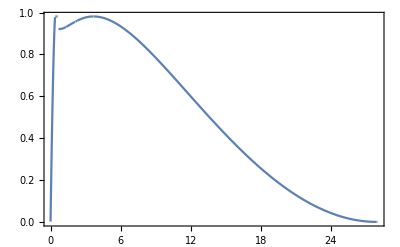

```mathematica
(*Plot[Integr[q0,1000,1000,0.4],{q0,0,28},Frame->True,PlotRange->Full]*)
```

```mathematica
100GeV
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

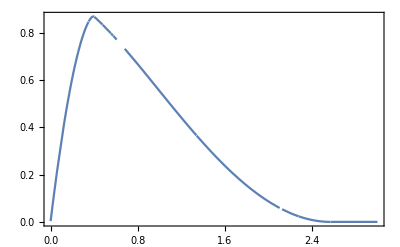

```mathematica
(*Plot[Integr[q0,100,1000,0.4],{q0,0,3},Frame->True,PlotRange->Full]*)
```

```mathematica
10GeV
```

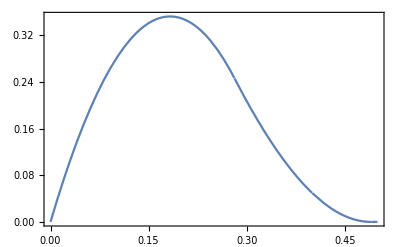

```mathematica
(*Plot[Integr[q0,10,1000,0.4],{q0,0,0.5},Frame->True,PlotRange->Full]*)
```

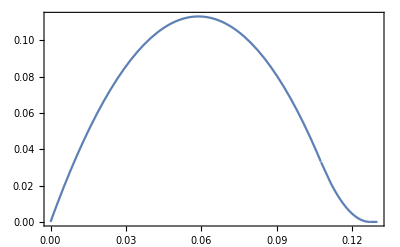

```mathematica
Plot[Integr[q0,1,1000,0.4],{q0,0,0.13},Frame->True,PlotRange->Full]
```

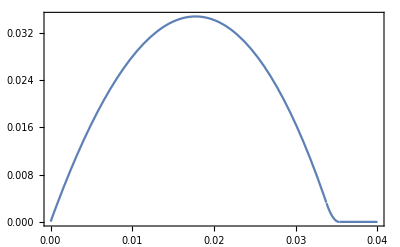

```mathematica
Plot[Integr[q0,0.1,1000,0.4],{q0,0,0.04},Frame->True,PlotRange->Full]
```

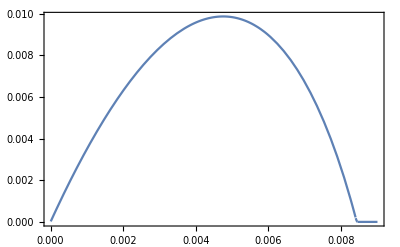

```mathematica
Plot[Integr[q0,0.01,1000,0.4],{q0,0,0.009},Frame->True,PlotRange->Full]
```

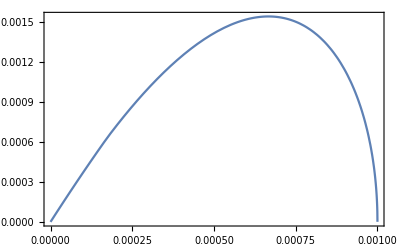

```mathematica
Plot[Integr[q0,1/10^3,1000,0.4],{q0,0,1/10^3},Frame->True,PlotRange->Full]
```

## Spectrums, mχ=100GeV (*shape depends mostly on T/mχ*)

```mathematica
(*100GeV*)
```

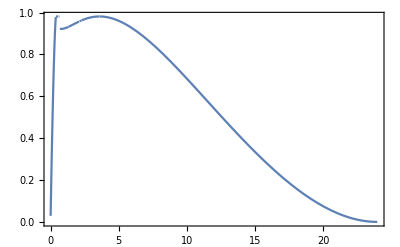

```mathematica
Plot[Integr[q0,100,100,0.4],{q0,0,24},Frame->True,PlotRange->Full]
```

```mathematica
(*10GeV*)
```

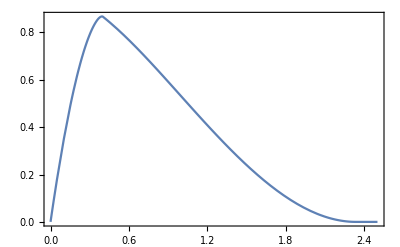

```mathematica
Plot[Integr[q0,10,100,0.4],{q0,0,2.5},Frame->True,PlotRange->Full]
```

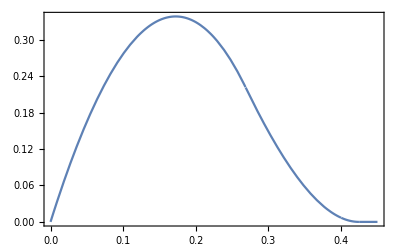

```mathematica
Plot[Integr[q0,1,100,0.4],{q0,0,0.45},Frame->True,PlotRange->Full]
```

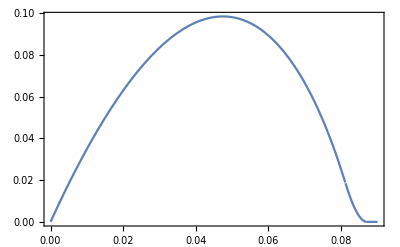

```mathematica
Plot[Integr[q0,0.1,100,0.4],{q0,0,0.09},Frame->True,PlotRange->Full]
```

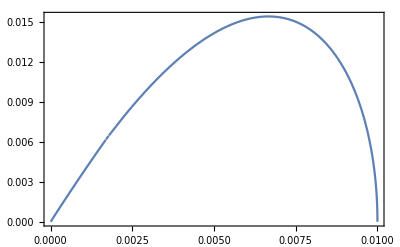

```mathematica
Plot[Integr[q0,0.01,100,0.4],{q0,0,0.01},Frame->True,PlotRange->Full]
```